```mathematica
ClearAll["Global`*"];
```

```mathematica
dir=NotebookDirectory[];
inputFile=FileNameJoin[{dir,"s2_L2_La0_11.txt"}];
lines=Import[inputFile,"Lines"];
data=Cases[StringSplit/@lines,{k_,re_,im_,___}/;StringMatchQ[k,DigitCharacter..]:>ToExpression/@{k,re,im}];
stableModes=data[[All,{2,3}]];
```

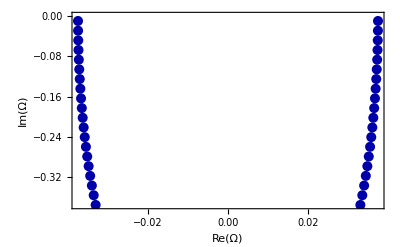

```mathematica
s2L2Lambda11=ListPlot[stableModes,PlotRange->All,PlotTheme->"Scientific",PlotStyle->{PointSize[0.018],Darker[Blue]},GridLines->None,FrameStyle->Directive[Black],FrameLabel->{Style[ToExpression["\\text{Re}[\\Omega]",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->14],Style[ToExpression["\\text{Im}[\\Omega]",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->14]},FrameTicksStyle->Directive[FontSize->13,Black,FontFamily->"TeX Gyre Pagella"]]
```

```mathematica
Export[FileNameJoin[{dir,"s2L2Lambda11.pdf"}],s2L2Lambda11];
```

```mathematica
(* NARIAI PLOTS *)
```

```mathematica
dir=NotebookDirectory[];
inputFile=FileNameJoin[{dir,"Ns_2_L_2.txt"}];
lines=Import[inputFile,"Lines"];
data=Cases[StringSplit/@lines,{k_,re_,im_,___}/;StringMatchQ[k,DigitCharacter..]:>ToExpression/@{k,re,im}];
stableModes=data[[All,{2,3}]];
```

```mathematica
analyticModes=(*L-2*)Flatten[Table[{{Sqrt[15]/2,-(n+1/2)},{-Sqrt[15]/2,-(n+1/2)}},{n,0,19}],1];(*L=1 Flatten[Table[{{Sqrt[7]/2,-(n+1/2)},{-Sqrt[7]/2,-(n+1/2)}},{n,0,19}],1];*)
```

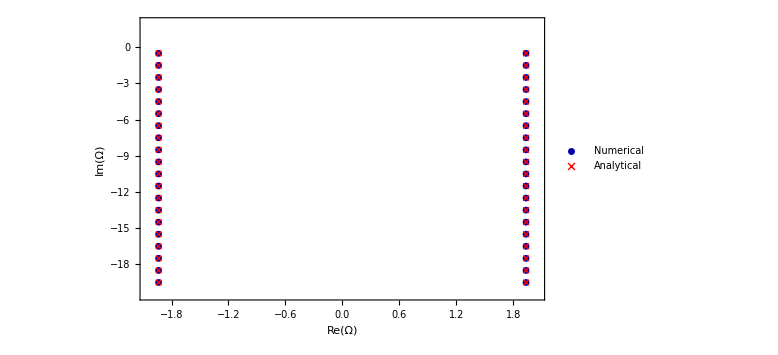

```mathematica
Nariais2L2Lambda11=ListPlot[{stableModes,analyticModes},PlotRange->{{-2.05,2.05},{-20.5,2}},PlotTheme->"Scientific",PlotStyle->{Directive[Darker[Blue],PointSize[0.018]],Directive[Red]},PlotMarkers->{{Automatic,7},{Style["×",Bold],20}},GridLines->None,FrameStyle->Directive[Black],FrameLabel->{Style[ToExpression["\\text{Re}[\\Omega]",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->15],Style[ToExpression["\\text{Im}[\\Omega]",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->15]},FrameTicksStyle->Directive[FontSize->13,Black,FontFamily->"TeX Gyre Pagella"],PlotLegends->Placed[LineLegend[{Style[ToExpression["Numerical",TeXForm,HoldForm],Black,FontSize->11,FontFamily->"TeX Gyre Pagella"],Style[ToExpression["Analytical",TeXForm,HoldForm],Black,FontSize->11,FontFamily->"TeX Gyre Pagella"]},LegendLayout->"Row"],{{0.7,0.94}}]]
```

```mathematica
Export[FileNameJoin[{dir,"Nariais2L2Lambda11.pdf"}],Nariais2L2Lambda11];
```